```mathematica
Fs = k l (Sin[θ2[t]] - Sin[θ1[t]])
exprs = {
m L^2 θ1''[t] == -m g L Sin[θ1[t]] + Fs l Cos[θ1[t]],
m L^2 θ2''[t] == -m g L Sin[θ2[t]] - Fs l Cos[θ2[t]],
θ1[0] == θ10, θ2[0] == θ20,
θ1'[0] == 0, θ2'[0] == 0
}
SetAttributes[{m, g, L , l, k}, Constant]
$Assumptions = {m > 0, g > 0, L > 0, l > 0, k > 0, Element[t, Reals]};
```

k l (-Sin[θ1[t]]+Sin[θ2[t]])

{L^2 m θ1''[t]==-g L m Sin[θ1[t]]+k l^2 Cos[θ1[t]] (-Sin[θ1[t]]+Sin[θ2[t]]),L^2 m θ2''[t]==-g L m Sin[θ2[t]]-k l^2 Cos[θ2[t]] (-Sin[θ1[t]]+Sin[θ2[t]]),θ1[0]==θ10,θ2[0]==θ20,θ1'[0]==0,θ2'[0]==0}

```mathematica
solns = FullSimplify@Refine@ComplexExpand@DSolve[Evaluate[exprs /. {Sin[a_] -> a, Cos[a_] -> 1}], {θ1[t], θ2[t]}, t][[1]]
```

{θ1[t]→1/2 ((θ10+θ20) Cos[√(g/L) t]+(θ10-θ20) Cos[(√(g L+(2 k l^2)/m) t)/L]),θ2[t]→1/2 ((θ10+θ20) Cos[√(g/L) t]+(-θ10+θ20) Cos[(√(g L+(2 k l^2)/m) t)/L])}

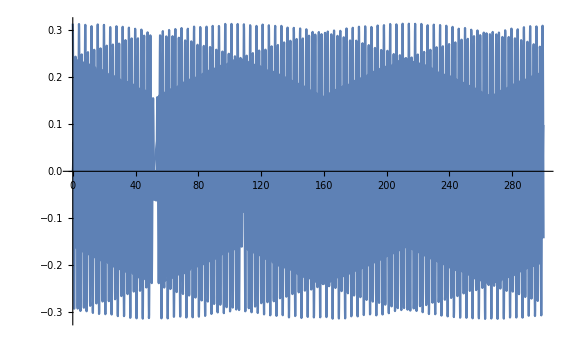
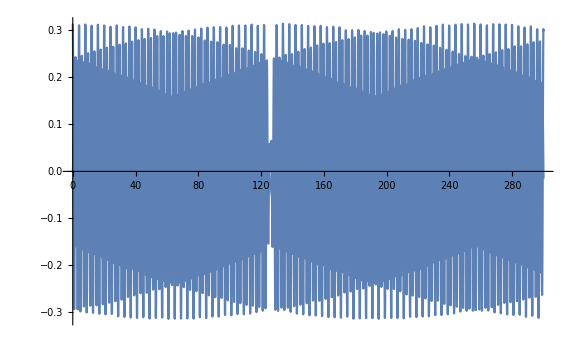

```mathematica
params = {
m -> 1.02`30,
g -> 9.797`30,
L -> 0.976`30,
l -> 0.93`30,
k -> 3.106`30,
θ10 -> 0,
θ20 -> Pi/10
};
tEnd = 300;
approxSolns = ReleaseHold[Hold[Compile[{{t, _Real}}, {θ1[t], θ2[t]}]] /. solns /. params];
exactSolns = ReleaseHold[Hold[Compile[{{t, _Real}}, {θ1[t], θ2[t]}]] /. NDSolve[
exprs /. params, {θ1, θ2}, {t, 0, tEnd},
AccuracyGoal->20, PrecisionGoal->20, WorkingPrecision->25,
MaxSteps->1000000
][[1]]];
{
Plot[approxSolns[t], {t, 0, tEnd}, ImageSize->Large],
Plot[exactSolns[t], {t, 0, tEnd}, ImageSize->Large]
}
```

```mathematica
addNoise[list_, scale_, q_] := Round[RandomFunction[WhiteNoiseProcess[], {0, Length[list] - 1}]["ValueList"][[1]] scale + list, Max@Abs[list] / q];approxData = addNoise[#1, 1/70, 12] & /@ Transpose@Table[approxSolns[t], {t, 0, 200, 1/sampleRate}];
exactData = addNoise[#1, 1/70, 12] & /@ Transpose@Table[exactSolns[t], {t, 0, 200, 1/sampleRate}];
```